The basic average of the amplitude over t

```mathematica
invmean=1/T Integrate[1/Exp[-t λ],{t,0,T}]
```

(-1+ⅇ^(T λ))/(T λ)

```mathematica
mean=1/T Integrate[Exp[-t λ],{t,0,T}]
```

(1-ⅇ^(-T λ))/(T λ)

Lets weight the average by the variance which is proportional to (1/a)^2

```mathematica
wmean=Integrate[Exp[-t λ]/((1/Exp[-t λ])^2),{t,0,T}]/Integrate[(1/Exp[-t λ])^2,{t,0,T}]
```

-(2 (-1+ⅇ^(-3 T λ)))/(3 (-1+ⅇ^(2 T λ)))

```mathematica
N[{mean,wmean}/.{T->0.1,λ->1}]
```

{0.951626,0.780423}

Lets weight the inverse  amplitude average by the variance which is proportional to (1/a)^2

```mathematica
invwmean=Integrate[1/Exp[-t λ]/((1/Exp[-t λ])^2),{t,0,T}]/Integrate[(1/Exp[-t λ])^2,{t,0,T}]
```

(2 (1-ⅇ^(-T λ)))/(-1+ⅇ^(2 T λ))

```mathematica
invwmean2=Integrate[1/Exp[-t λ]/((1/Exp[-t λ])),{t,0,T}]/Integrate[(1/Exp[-t λ]),{t,0,T}]
```

(T λ)/(-1+ⅇ^(T λ))

```mathematica
N[{1/mean,invmean,1/wmean,invwmean,invwmean2}/.{T->4.2,λ->1}]
```

{4.26394,15.6396,2256.88,0.00044309,0.0639402}

```mathematica
scal=1/(T mean)
```

λ/(1-ⅇ^(-T λ))

```mathematica
Limit[scal,T->∞]
```

ConditionalExpression[λ, λ>0]

```mathematica
Solve[(scal-λ)/λ==0.1,T]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{T→2.3979/λ}}

2

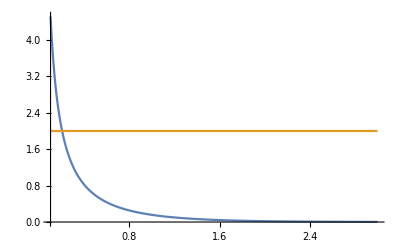

```mathematica
lmbdatmp=2
Plot[{{(scal-λ)/λ}/.{λ->lmbdatmp},lmbdatmp},{T,0.1,3},PlotRange->All]
```

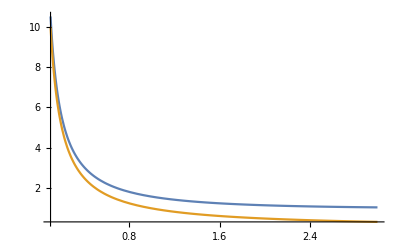

```mathematica
Plot[{{scal}/.{λ->1},1/T},{T,0.1,3},PlotRange->All]
```

2

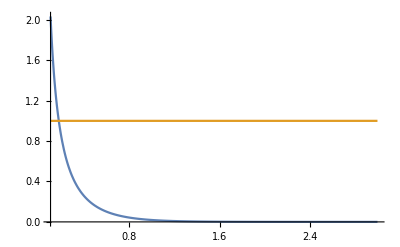

```mathematica
lmbdatmp=2
Plot[{{(scal-λ)/λ}/.{λ->lmbdatmp,T-> t*lmbdatmp},1},{t,0.1 ,3 },PlotRange->All]
```

```mathematica
√(1/Subscript[N, t])
```